# Eyeglass Flasher 13 (ma8)

This notebook explores Eyeglass structures based on the Shafer/Palmer flasher, but with adjustments to put finite space between cylindrical layers while keeping triangular facets flat in both the CP and the FF.

This version of the notebook is designed for Mathematica version 8. It is entirely rewritten from earlier versions.

Version 12a has a few more sample cases worked out.

Version 13 incorporates the flat-bottom condition into the solution analysis and also cleans up the documentation.

All functions are described and defined below. To load all functions, select the entire notebook and hit “Enter.” This will load all of the function and execute all of the examples, including the examples included in the paper. To see more extensive examples, in the Setup->Setup section immediately below, set the $ShowExample variable to True before executing the notebook.

## Setup

### Setup

#### Off[General::spell, General::spell1] Default AspectRatio, PlotRange in Graphics ShowExample[x], $ShowExample, SetShowExample[f] PrintThis[x]

Turn off spelling messages we don't care about.

```mathematica
Off[General::spell,General::spell1];
```

Make all plots with automatic aspect ratios and plot all points.

```mathematica
SetOptions[Graphics, AspectRatio->Automatic, PlotRange->All];
```

```mathematica
SetOptions[Graphics3D,Boxed->False,PlotRange->All];
```

ShowExample[x] executes its arguments if and only if the global variable $ShowExample is set to True. I use this to turn on and off display of examples for this entire notebook.
SetShowExample[f] turns on or off display of ShowExample[]'s arguments.

```mathematica
$ShowExample=False;
```

```mathematica
ShowExample[x_]:=If[$ShowExample,x]
```

```mathematica
SetAttributes[ShowExample,HoldFirst];
```

```mathematica
SetShowExample[f_]:=$ShowExample=f;
```

PrintThis[x] is a function used in debugging that takes an expression and prints to the console the display form of the expression x and its value, and then returns the evaluated value of x as its return value. It's particularly useful because you can temporarily insert "PrintThis@" before an expression to display it without otherwise altering the flow of the function. However, since it returns a copy of the return value, you can't apply PrintThis to an lvalue (e.r., the argument of Set or AppendTo).

```mathematica
PrintThis[x_]:=With[{y=x},Print[HoldForm[x]," = ",y];y]
```

```mathematica
SetAttributes[PrintThis,HoldFirst];
```

Example

```mathematica
(foo=1;PrintThis[++foo])//ShowExample
```

#### U[ϕ]

U[ϕ] returns a 2-D unit vector at angle ϕ.

```mathematica
U[ϕ_]:={Cos[ϕ],Sin[ϕ]};
```

#### Mag2[v] Mag[v]

Mag2[v] returns the magnitude squared of a vector v.

```mathematica
Mag2[v_]:=Plus@@(v^2);
```

Example

```mathematica
Mag2[{1,1,1}]
```

3

Mag[v] returns the magnitude of a vector v.

```mathematica
Mag[v_]:=√Mag2[v]
```

### Eyeglass Flasher

#### Notes

In this section, we set up variables and functions that allow the design and visualization of flashers. A flasher design can be characterized by several parameters:
	r - is the number of rings, i.e., the number of up-and-down layers in each half-sector, or, equivalently, the number of segments in each radial diagonal.
	h - is the height order. The desired height of the folded form is h panels, i.e., each ring is h panels high. h is also the number of turns a diagonal makes going from bottom to top.
	m - is the rotational order. m=4 for square, 6 for hexagonal, and so forth.
	n - is the radial order. It’s the number of “natural” panel increments there are in the CP. So n = r × h.
Those are all integers. There is also one floating-point value:
	dr - is the radial increment. Basically, vertices at the same height in the folded form are spaced radially by this amount (relative to the radial distance of the corresponding inner polygon vertex). This is the value that results in the imperfect symmetry of the crease pattern; the larger the value of dr, the faster that outer rings grow in height and the more “curved” are the diagonal folds.

We analyze a flasher by parameterizing the vertices of its crease pattern (CP) and folded form (FF). We place constraints on the vertices of the folded form, then solve for the vertices of the CP in such a way that we enforce isometry between the CP and FF.

#### Points and their components p_(i, j, k), pp_(i, j, k) R[k, m], RR[k, m]

Points in a crease pattern of order n are vectors of the form p_(i,j, k) for  i=0,...,n, j=0,...,n, k=0...m-1, where i, j are indices of the point position within a single sector and k specifies the rotational position. Because of symmetry, we only need to parameterize a single sector of points.

Because we claim these two symbols for ourselves, we will squawk if anyone tries to assign a value to them.

```mathematica
Protect[p,pp];
```

A key concept is that the indices wrap around from one rotational sector to the next, so there is a natural definition for i=-1 subscript.

```mathematica
Subscript[p, -1,j_,k_]:=Subscript[p, j,0,k-1]
```

```mathematica
Subscript[pp, -1,j_,k_]:=Subscript[pp, j,0,k-1]
```

Here are the points of a single sector, which illustrate this wrap-around behavior. (The central polygon is incident to the bottom edge, rightmost segment.)

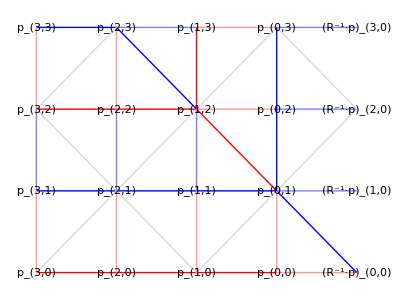

Corresponding points in the folded form have the same subscripts but have head pp. Here are the points of a single sector in 3D, plus how all four sectors go together to create the entire flasher.

-Graphics-

These aren’t accurate, of course; they’re drawings that are close to the proper vertex positions. The goal of this notebook is to solve for what those vertex positions actually are.

R[k, m] returns the 2D rotation matrix for (k/m) turns about the origin.

```mathematica
R[k_,m_]:={{Cos[2π k/m],-Sin[2π k/m]},{Sin[2π k/m],Cos[2π k/m]}}
```

RR[k, m] returns the 3D rotation matrix for (k/m) turns about the z axis.

```mathematica
RR[k_,m_]:={{Cos[2π k/m],-Sin[2π k/m],0},{Sin[2π k/m],Cos[2π k/m],0},{0,0,1}}
```

#### Crease pattern coordinates RulesCP[m]

RulesCP[m] returns a rule that maps any 2D vertex p_(i, j, k) to its desired position in the CP for rotational order m.

```mathematica
RulesCP[m_]:={Subscript[p, i_,j_,k_]:>R[k,m].N[1/2{Cot[π/m],1}+If[i+1≥j,(i+1) U[π/2+(2π)/m]+Tan[π/m]j U[(2π)/m],j U[π/2]-Tan[π/m](i+1)U[0]]]}
```

Example: central polygon.

```mathematica
Subscript[p, 0,0,0]/.RulesCP[4]
```

{-0.5,0.5}

#### BorderFold SharpFold[f] MedFold[f] LightFold

Color-coding for crease types. There are three weights of creases, each of which may come in either mountain or valley parity. We'll make functions that return the color for each type.

BorderFold is the border of the pattern.

```mathematica
BorderFold:=Black
```

SharpFold[f] is the color for a sharp fold, one that is around 180°. The type (signified by hue) is set by the parity variable f: even = valley (red), odd = mountain (blue). Sharp folds are darker than the other two flavors.

```mathematica
SharpFold[f_]:=If[Mod[f,2]==0,RGBColor[1,0,0],RGBColor[0,0,1]]
```

MedFold[p] is the color for a medium fold, one that is around 90°. As with SharpFold[], the type (signified by hue) is set by the parity variable p. Medium folds are lighter than sharp folds.

```mathematica
MedFold[f_]:=If[Mod[f,2]==0,RGBColor[1,.7,.7],RGBColor[.6,.6,1]]
```

LightFold is the color for a light fold, one that is around 0° (a slight bend). Since the direction of a light fold is not generally known, we do not give it a type and we use light gray for the color.

```mathematica
LightFold := GrayLevel[.85]
```

#### Generalized labels PtLabel[v_(i,j,k)] FlasherFirstSectorLabelsAll[v, n] FlasherSectorFolds[v, r, h, k] FlasherSectorQuads[v, r, h, k] FlasherSectorTriangles[v, r, h, k] FlasherSectorDiags[v, r, h, k] FlasherSectorDiagsX[v, r, h, k] FlasherSector[v, r, h, k] FlasherSectorPolys[v, r, h, k] Flasher[v, r, h, m] FlasherPolys[v, r, h, m] FlasherFirstSectorVertices[v, r, h] FlasherFirstSectorVerticesDistinct[v, r, h] FlasherPair[v, r, h, m]

This section constructs graphical representations of portions of flashers in 2D (crease pattern, CP) and 3D (folded form, FF).

We’ll construct a single representation of the fold pattern for a single sector that describes the structure of both the crease pattern and the folded form. Three parameters characterize the structure topologically:{r, h, m}, where r is the number of “rings” (basically, the number of up-and-down layers), h is the height order (the number of basic panels in each up-and-down layer), and m is the rotationally symmetry. For sector-specific functions, k is the rotational index of the particular sector.

First, some labels so we know what we’re looking at.

PtLabel[v_(i,j,k)] takes a subscripted point (p or pp) and returns a label at its position.

```mathematica
PtLabel[Subscript[v_, i_,j_,k_]]:=Text[Subscript[Style[ToString[v],Bold], i,j,k],Subscript[v, i,j,k]]
```

FlasherFirstSectorLabelsAll[v, n] returns a set of labels for all points in the first (k=0) sector up to the nth ring.

```mathematica
FlasherFirstSectorLabelsAll[v_,n_]:=Style[Table[PtLabel[Subscript[v, i,j,0]],{i,-1,n},{j,0,n}],Black]
```

Example

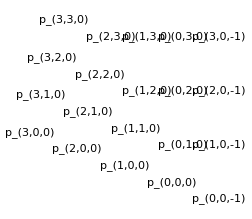

```mathematica
With[{n=3,m=5},Graphics[FlasherFirstSectorLabelsAll[p,n]/.RulesCP[m]]]
```

FlasherSectorFolds[v, r, h, k] returns a list of fold lines for the sharp and medium folds, but doesn’t include any light folds.

```mathematica
FlasherSectorFolds[v_,r_,h_,k_]:=Module[{n,i,j},
n=r*h;(* total number of radial increments *)
Flatten[{
(* major region *)
Table[{j=h*ig;
Style[Line[{Subscript[v, i,j,k],Subscript[v, i-1,j,k]}],SharpFold[ig]],(* bottom of quadrant *)
Style[Line[{Subscript[v, i,j,k],Subscript[v, i,Min[j+h,i+1],k]}],If[i==n,BorderFold,MedFold[ig]]](* left of quadrant *)
},{ig,0,r-1},{i,h*ig,n}],
Style[Line[{Subscript[v, n,h*r,k],Subscript[v, n-1,h*r,k]}],BorderFold],(* extra segment at corner *)
(* diagonal *)
Table[{i=h*ig+j;
Style[Line[{Subscript[v, i-1,i,k],Subscript[v, i,i+1,k]}],SharpFold[ig+1]]
},{ig,0,r-1},{j,0,h-1}],
(* minor region *)
Table[{i=h*ig-1;
If[ig≠0,Style[Line[{Subscript[v, i,j,k],Subscript[v, i,j-1,k]}],SharpFold[ig]],{}],(* bottom of quadrant *)
Style[Line[{Subscript[v, i,j,k],Subscript[v, Min[i+h,j-1],j,k]}],If[j==n,BorderFold,MedFold[ig+1]]](* left of quadrant *)
},{ig,0,r-1},{j,h*ig+1,n}]
}]
]
```

Example

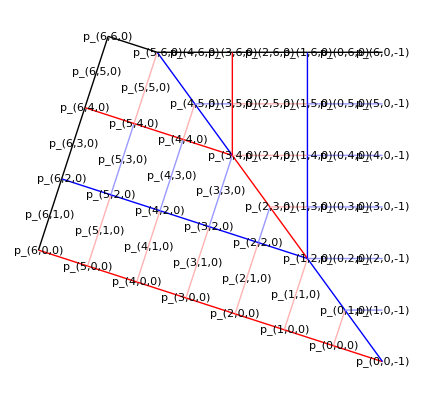

```mathematica
Module[{r=3,h=2,n,m=5,k=0},
n=r*h;
Graphics[{
FlasherSectorFolds[p,r,h,k],
FlasherFirstSectorLabelsAll[p,n]
}/.RulesCP[m]]]
```

FlasherSectorQuads[v, r, h, k] returns a list of vertex quadruplets for the quadrilateral facets in this order:
	bottom-outside
	bottom-inside
	top-inside
	top-outside
So that in the major region, the vertices cycle counterclockwise and in the minor region they cycle clockwise. The quads are significant because each quad can be triangulated in two ways.

```mathematica
FlasherSectorQuads[v_,r_,h_,k_]:=Module[{n,i,j,quad},
n=r*h;(* total number of radial increments *)
Flatten[{
(* major region *)
Table[{j=h*ig;
If[Min[j+h,i]>j,quad[Subscript[v, i,j,k],Subscript[v, i-1,j,k],Subscript[v, i-1,Min[j+h,i],k],Subscript[v, i,Min[j+h,i+1],k]],{}]
},{ig,0,r-1},{i,h*ig,n}],
(* minor region *)
Table[{i=h*ig-1;
If[Min[i+h,j-2]>i,quad[Subscript[v, i,j,k],Subscript[v, i,j-1,k],Subscript[v, Min[i+h,j-2],j-1,k],Subscript[v, Min[i+h,j-1],j,k]],{}]
},{ig,0,r-1},{j,h*ig+1,n}]
}]/.quad->List
]
```

Example. Display and number the quads.

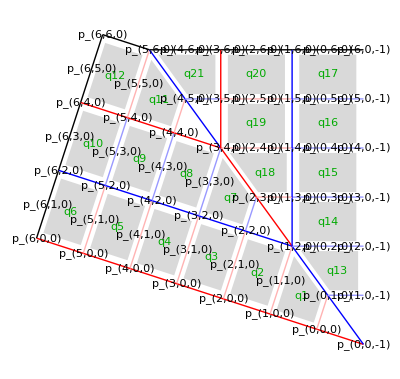

```mathematica
Module[{r=3,h=2,m=5,fsq,fspolys},
fsq=FlasherSectorQuads[p,r,h,0];
fspolys=MapIndexed[With[{ctr=Plus@@#1/4},{Style[Polygon[ctr+0.8(#1-ctr)],LightGray],Style[Text["q"<>ToString[#2⟦1⟧],ctr],Darker[Green]]}]&,fsq];
Graphics[{fspolys,FlasherSectorFolds[p,r,h,0],FlasherFirstSectorLabelsAll[p,r*h]}/.RulesCP[m]]
]
```

FlasherSectorTriangles[v, r, h, k] returns a list of vertex triplets for the triangle facets in this order:
	bottom-outside
	bottom-inside
	top-inside
	top-outside
So that in the major region, the vertices cycle counterclockwise and in the minor region they cycle clockwise. Note that we build this function by duplicating the quad function and editing slightly. When the strict inequalities of the latter reach equality (the former), we get a triangle.

```mathematica
FlasherSectorTriangles[v_,r_,h_,k_]:=Module[{n,i,j,quad},
n=r*h;(* total number of radial increments *)
Flatten[{
(* major region *)
Table[{j=h*ig;
If[Min[j+h,i]==j,quad[Subscript[v, i,j,k],Subscript[v, i-1,j,k],Subscript[v, i,Min[j+h,i+1],k]],{}]
},{ig,0,r-1},{i,h*ig,n}],
(* minor region *)
Table[{i=h*ig-1;
If[Min[i+h,j-2]==i,quad[Subscript[v, i,j,k],Subscript[v, i,j-1,k],Subscript[v, Min[i+h,j-1],j,k]],{}]
},{ig,0,r-1},{j,h*ig+1,n}]
}]/.quad->List
]
```

Example. Display and number the triangles.

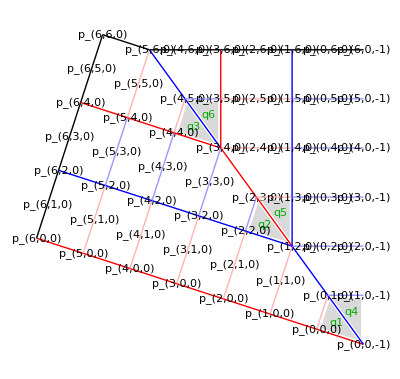

```mathematica
Module[{r=3,h=2,m=5,fsq,fspolys},
fsq=FlasherSectorTriangles[p,r,h,0];
fspolys=MapIndexed[With[{ctr=Plus@@#1/3},{Style[Polygon[ctr+0.8(#1-ctr)],LightGray],Style[Text["q"<>ToString[#2⟦1⟧],ctr],Darker[Green]]}]&,fsq];
Graphics[{fspolys,FlasherSectorFolds[p,r,h,0],FlasherFirstSectorLabelsAll[p,r*h]}/.RulesCP[m]]
]
```

FlasherSectorDiags[v, r, h, k] returns a list of the diagonal folds that cross each quadrant. There are two ways to cross each quadrant, of course, so there are many ways to create the diagonals (and the different ways set which direction each panel flexes in the folded form and/or during deployment). This assignment is consistent relative to the quad position and splits the obtuse angles and, because of its consistent direction, insures that there are never any interior degree-4 vertices.

```mathematica
FlasherSectorDiags[v_,r_,h_,k_]:=Module[{fsq},
fsq=FlasherSectorQuads[v,r,h,k];
Style[Line[#⟦{1,3}⟧],LightFold]&/@fsq
]
```

Example

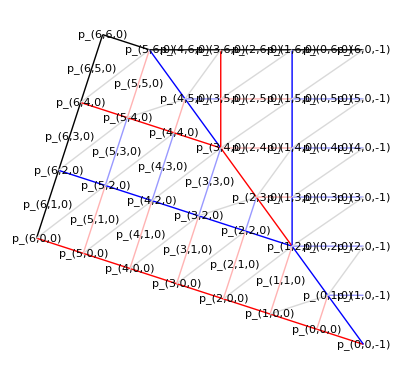

```mathematica
Module[{r=3,h=2,n,m=5,k=0},
n=r*h;
Graphics[{
FlasherSectorFolds[p,r,h,k],
FlasherSectorDiags[p,r,h,k],
FlasherFirstSectorLabelsAll[p,n]
}/.RulesCP[m]]]
```

FlasherSectorDiagsX[v, r, h, k] returns a different arrangment of the diagonal folds, which is the version that I used in my initial analysis. (So using this pattern, we should be able to reproduce the previous analysis.) Note that the way I construct this pattern relies on the order that the quads were built.

```mathematica
FlasherSectorDiagsX[v_,r_,h_,k_]:=Module[{fsq,nmajor,nminor,qmajor,qminor,qrmajor,qrminor,n},
fsq=FlasherSectorQuads[v,r,h,k];
nmajor=(Length[fsq]+r)/2;(* number in first row of major region *)
nminor=nmajor-r;(* number in first row of minor region *)
qmajor=Take[fsq,nmajor];(* the major quads *)
qminor=Take[fsq,-nminor];(* the minor quads *)
(* now partition into individual rows *)
qrmajor = {};n=r*h;(* number of elements in major row *)
While[n>0,AppendTo[qrmajor,Take[qmajor,n]];qmajor=Drop[qmajor,n];n-=h];
qrminor={};n=r*h-1;(* number of elements in 1st minor row *)
While[n>0,AppendTo[qrminor,Take[qminor,n]];qminor=Drop[qminor,n];n-=h];
Flatten[Join[MapIndexed[Style[Line[If[Mod[#2⟦2⟧+(h-1)*(#2⟦1⟧-1)+1,2]==0,#1⟦{1,3}⟧,#1⟦{2,4}⟧]],LightFold]&,qrminor,{2}],
MapIndexed[Style[Line[If[Mod[#2⟦2⟧+(h-1)*(#2⟦1⟧-1)+1,2]==0,#1⟦{1,3}⟧,#1⟦{2,4}⟧]],LightFold]&,qrmajor,{2}]]]
]
```

Example

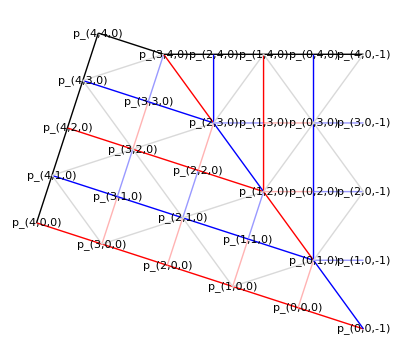

```mathematica
Module[{r=4,h=1,n,m=5,k=0},
n=r*h;
Graphics[{
FlasherSectorFolds[p,r,h,k],
FlasherSectorDiagsX[p,r,h,k],
FlasherFirstSectorLabelsAll[p,n]
}/.RulesCP[m]]]
```

FlasherSector[v, r, h, k] returns a flat list of both fold lines and diagonal lines. (Note that you can substitute a different diagonal pattern if you like at this point.)

```mathematica
FlasherSector[v_,r_,h_,k_]:=Join[
FlasherSectorFolds[v,r,h,k],
FlasherSectorDiags[v,r,h,k]
]
```

Example

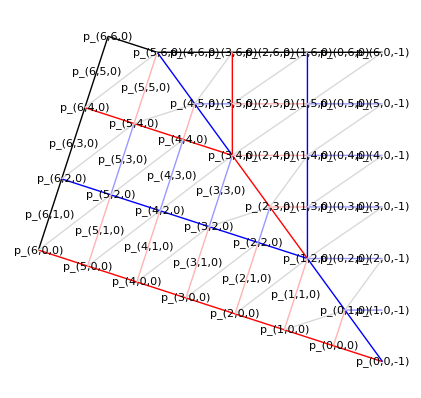

```mathematica
Module[{r=3,h=2,n,m=5,k=0},
n=r*h;
Graphics[{FlasherSector[p,r,h,k],FlasherFirstSectorLabelsAll[p,n]}/.RulesCP[m]]]
```

FlasherSectorPolys[v, r, h, k] returns a flat list of Polygons for the flasher. Used to build a solid model. Note that the quadrilaterals can be skew in the folded form, and we don’t try to make their diagonals match the ones in FlasherSectorDiag.

```mathematica
FlasherSectorPolys[v_,r_,h_,k_]:=
Polygon/@Join[FlasherSectorQuads[v,r,h,k],FlasherSectorTriangles[v,r,h,k]]
```

Example (this is much more useful in the folded form)

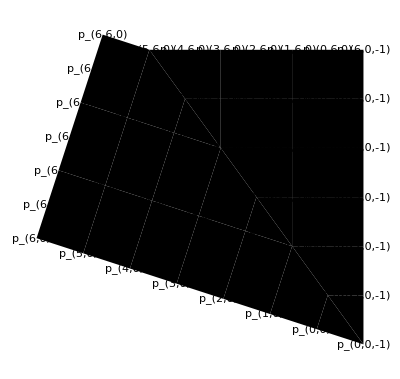

```mathematica
Module[{r=3,h=2,n,m=5,k=0},
n=r*h;
Graphics[{FlasherSectorPolys[p,r,h,k],FlasherFirstSectorLabelsAll[p,n]}/.RulesCP[m]]]
```

Flasher[v, r, h, m] returns the line pattern for the full flasher of rotational order m.

```mathematica
Flasher[v_, r_,h_,m_]:=Table[FlasherSector[v,r,h,k],{k,0,m-1}]
```

Example

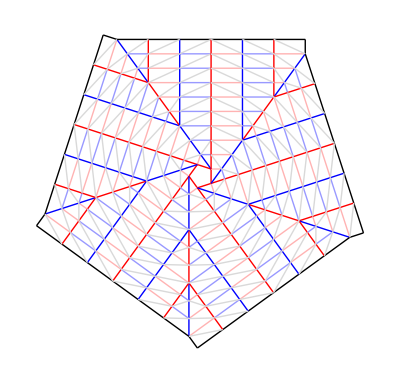

```mathematica
Module[{r=3,h=3,m=5},
Graphics[{Flasher[p,r,h,m]}/.RulesCP[m]]]
```

FlasherPolys[v, r, h, m] returns Polygons for the full flasher of rotational order m. Note that we have to add the central polygon.

```mathematica
FlasherPolys[v_, r_,h_,m_]:=Join[Table[FlasherSectorPolys[v,r,h,k],{k,0,m-1}],{Polygon[Table[Subscript[v, 0,0,k],{k,0,m-1}]]}]
```

Example. Again, better seen as folded form than CP.

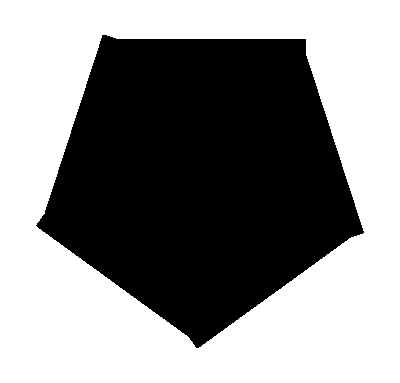

```mathematica
Module[{r=3,h=3,m=5},
Graphics[{FlasherPolys[p,r,h,m]}/.RulesCP[m]]]
```

FlasherFirstSectorVertices[v, r, h] returns a list of all of the vertex variables of type v that appear in the first sector of the specified Flasher pattern.

```mathematica
FlasherFirstSectorVertices[v_,r_,h_]:=Union[Cases[{FlasherSector[v,r,h,0]},Subscript[v, ___],∞]]
```

Example

```mathematica
Module[{r=3,h=3},
FlasherFirstSectorVertices[p,r,h]]
```

{p_(0,0,-1),p_(0,0,0),p_(0,1,0),p_(1,0,-1),p_(1,0,0),p_(1,2,0),p_(2,0,-1),p_(2,0,0),p_(2,3,0),p_(2,4,0),p_(2,5,0),p_(2,6,0),p_(2,7,0),p_(2,8,0),p_(2,9,0),p_(3,0,-1),p_(3,0,0),p_(3,3,0),p_(3,4,0),p_(4,0,-1),p_(4,0,0),p_(4,3,0),p_(4,5,0),p_(5,0,-1),p_(5,0,0),p_(5,3,0),p_(5,6,0),p_(5,7,0),p_(5,8,0),p_(5,9,0),p_(6,0,-1),p_(6,0,0),p_(6,3,0),p_(6,6,0),p_(6,7,0),p_(7,0,-1),p_(7,0,0),p_(7,3,0),p_(7,6,0),p_(7,8,0),p_(8,0,-1),p_(8,0,0),p_(8,3,0),p_(8,6,0),p_(8,9,0),p_(9,0,-1),p_(9,0,0),p_(9,3,0),p_(9,6,0),p_(9,9,0)}

Example -- same sector as above, but only label the vertices that actually appear in the pattern.

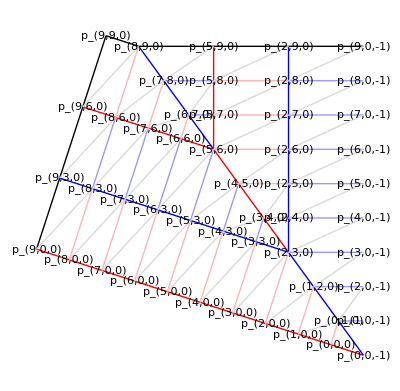

```mathematica
Module[{r=3,h=3,n,m=5},
Graphics[{FlasherSector[p,r,h,0],PtLabel/@FlasherFirstSectorVertices[p,r,h]}/.RulesCP[m]]]
```

Now, note that the k=-1 vertices are vertices that are rotated versions of the vertices from other sectors. When it comes time to set constraints, we’ll want to consider only those vertices that are uniquely associated with the first sector.

FlasherFirstSectorVerticesDistinct[v, r, h] returns just those vertices whose third index is zero.

```mathematica
FlasherFirstSectorVerticesDistinct[v_,r_,h_]:=Union[Cases[{FlasherSector[v,r,h,0]},Subscript[v, _,_,0],∞]]
```

Example

```mathematica
Module[{r=3,h=3},
FlasherFirstSectorVerticesDistinct[p,r,h]]
```

{p_(0,0,0),p_(0,1,0),p_(1,0,0),p_(1,2,0),p_(2,0,0),p_(2,3,0),p_(2,4,0),p_(2,5,0),p_(2,6,0),p_(2,7,0),p_(2,8,0),p_(2,9,0),p_(3,0,0),p_(3,3,0),p_(3,4,0),p_(4,0,0),p_(4,3,0),p_(4,5,0),p_(5,0,0),p_(5,3,0),p_(5,6,0),p_(5,7,0),p_(5,8,0),p_(5,9,0),p_(6,0,0),p_(6,3,0),p_(6,6,0),p_(6,7,0),p_(7,0,0),p_(7,3,0),p_(7,6,0),p_(7,8,0),p_(8,0,0),p_(8,3,0),p_(8,6,0),p_(8,9,0),p_(9,0,0),p_(9,3,0),p_(9,6,0),p_(9,9,0)}

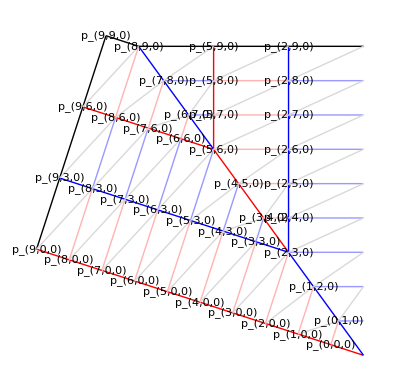

```mathematica
Module[{r=3,h=3,n,m=5},
Graphics[{FlasherSector[p,r,h,0],PtLabel/@FlasherFirstSectorVerticesDistinct[p,r,h]}/.RulesCP[m]]]
```

FlasherPair[v, r, h, m] returns a pair of lists of graphical elements that show the first sector, labeled, and the complete pattern, parameterized on vertex variable v, so that we can get both the CP and FF patterns.

```mathematica
FlasherPair[v_,r_,h_,m_]:={
{FlasherSector[v,r,h,0],PtLabel/@FlasherFirstSectorVertices[v,r,h]},
Flasher[v,r,h,m]}
```

Example

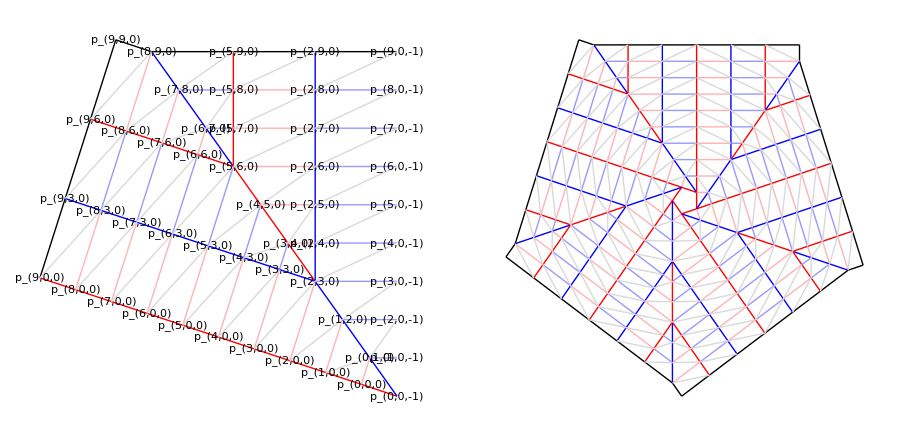

```mathematica
Module[{r=3,h=3,m=5},
GraphicsRow[Graphics/@FlasherPair[p,r,h,m]]/.RulesCP[m]
]
```

#### Crease pattern graphics FlasherPairGraphicsCP[r, h, m] FlasherPolyGraphicsCP[r, h, m] To3D[g]

FlasherPairGraphicsCP[r, h, m] returns a GraphicsRow containing the two Graphics representations of the labeled first sector and the full crease pattern, still parameterized on p_(i, j, k).

```mathematica
FlasherPairGraphicsCP[r_,h_,m_] :=GraphicsRow[Graphics/@FlasherPair[p,r,h,m]]
```

Example

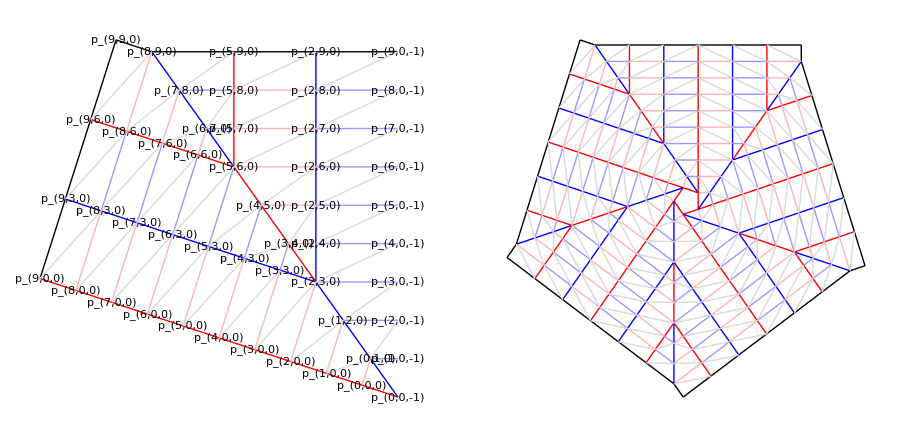

```mathematica
Module[{r=3,h=3,m=5},
FlasherPairGraphicsCP[r,h,m]/.RulesCP[m]
]
```

FlasherPolyGraphicsCP[r, h, m] returns a Graphics version of the crease pattern with Polygon faces. Useful for exporting a solid model.

```mathematica
FlasherPolyGraphicsCP[r_,h_,m_]:=Graphics[FlasherPolys[p,r,h,m]]
```

Example

```mathematica
Module[{r=3,h=3,m=5},
FlasherPolyGraphicsCP[r,h,m]/.RulesCP[m]
]
```

-Graphics-

To3D[g] takes a 2D Graphics object g and converts it to a flat Graphics3D object in the xy plane. You can use it to convert FlasherPolyGraphicsCP to a Graphics3D object. Note, though, that the points within must be fully rendered as 2-lists; if they are symbolic, they won’t get properly converted.

Also, right now we only implement this for Text, Line and Polygon objects. Add more objects as needed.

```mathematica
To3D[g_]:=g/.{
Graphics->Graphics3D,
Text[t_,p_,opts___]:>Text[t,Append[p,0],opts],
Line[x_]:>Line[Append[#,0]&/@x],
Polygon[x_]:>Polygon[Append[#,0]&/@x]
}
```

Example

```mathematica
Module[{r=3,h=3,m=5},
To3D[FlasherPolyGraphicsCP[r,h,m]/.RulesCP[m]]
]
```

-Graphics3D-

#### Folded form coordinates rot[i, j] rad[i, j] ud[i, j] ht[i, j, h] RulesFF[h, m, dr]

The points of a single sector of the pattern have two indices, i and j. There are a couple of useful functions of these indices that are used to compute the ideal folded form position.

rot[i, j] gives the number of times a point in the CP gets rotated in the folded form.

```mathematica
rot[i_,j_]:=If[j≤i+1,i+1,j]
```

Show this for a sector.

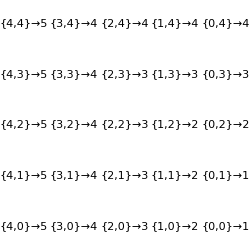

```mathematica
Graphics[Table[Text[{i,j}->rot[i,j],{-i,j}],{i,0,4},{j,0,4}]]
```

rad[i,j] gives the (dimensionless) desired radial displacement in the folded form.

```mathematica
rad[i_,j_]:=If[j≤i+1,i(i+1)+j,j(j+1)-(i+1)]
```

Show this for a sector.

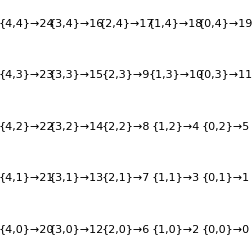

```mathematica
Graphics[Table[Text[{i,j}->rad[i,j],{-i,j}],{i,0,4},{j,0,4}]]
```

ud[i,j] returns a value 1 if the point pp_(i,j) is "up" and 0 if it is "down.” [OBSOLETE]

```mathematica
ud[i_,j_]:=1/2(1-(-1)^Min[i+1,j])
```

Show this for a sector.

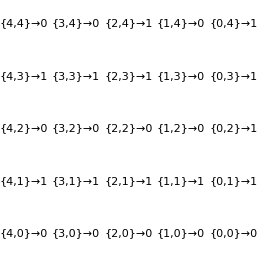

```mathematica
Graphics[Table[Text[{i,j}->ud[i,j],{-i,j}],{i,0,4},{j,0,4}]]
```

ht[i, j, h] returns the discrete height of pp_(i, j, k) in the folded form for panel height parameter h.

```mathematica
ht[i_,j_,h_]:=Abs[Mod[Min[i+1,j]-h,2h,0]-h]
```

Show this for a sector of height 2.

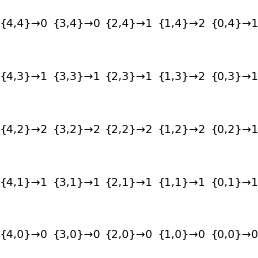

```mathematica
Graphics[Table[Text[{i,j}->ht[i,j,2],{-i,j}],{i,0,4},{j,0,4}]]
```

RulesFF[h, m, dr] returns a set of rules giving 3-dimensional coordinates for the points of the folded form for hieght order h, rotational order m, with dr being the radial spacing of the concentric layers within a given horizontal plane relative to the radial distance of the innermost vertex (central polygon). This is an idealized structure, and in general will not be isometric to a flat crease pattern. But we’ll use it as a starting point when we solve for the crease pattern.

```mathematica
RulesFF[h_,m_,dr_:.1]:={Subscript[pp, i_,j_,k_]:>N[RR[k+rot[i,j],m].(1/2(1+dr rad[i,j]/h){Cot[π/m],1,0}+{0,0, ht[i,j,h]Tan[π/m]})]}
```

Example: central polygon.

```mathematica
Subscript[pp, 0,0,0]/.RulesFF[1,4]
```

{-0.5,0.5,0.}

Example

```mathematica
Module[{r=3,h=3,m=4},
Graphics3D[FlasherSector[pp,r,h,0]/.RulesFF[h,m,0.01],Axes->True]]
```

-Graphics3D-

#### Folded form graphics FlasherPairGraphicsFF[r, h, m] FlasherPolyGraphicsFF[r, h, m]

FlasherPairGraphicsFF[r, h, m] returns a GraphicsRow containing the two Graphics3D representations of the labeled first secor and the full crease pattern, still parameterized on pp_(i, j, k).

```mathematica
FlasherPairGraphicsFF[r_,h_,m_] :=GraphicsRow[Graphics3D/@FlasherPair[pp,r,h,m]]
```

Example

```mathematica
Module[{r=3,h=3,m=5},
FlasherPairGraphicsFF[r,h,m]/.RulesFF[h,m]
]
```

-Graphics-

FlasherPolyGraphicsFF[r, h, m] returns a Graphics3D version of the folded form with Polygon faces. Useful for rending the faces, also for exporting a solid model.

```mathematica
FlasherPolyGraphicsFF[r_,h_,m_]:=Graphics3D[FlasherPolys[pp,r,h,m]]
```

Example

```mathematica
Module[{r=3,h=3,m=5},
FlasherPolyGraphicsFF[r,h,m]/.RulesFF[h,m]
]
```

-Graphics3D-

#### CP and FF together FlasherSetArray[r, h, m] FlasherSetGraphics[r, h, m]

FlasherSetArray[r, h, m] returns a 2-D List containing the two Graphics3D representations of the labeled first secor and the full crease pattern, still parameterized on p_(i, j, k), and four views of the folded form parameterized on pp_(i, j, k). Returned as a list of lists because it’s easier to pick out elements before it gets wrapped in GraphicsGrid.

```mathematica
FlasherSetArray[r_,h_,m_] :=Module[{cpset,ffset},
cpset=Graphics/@FlasherPair[p,r,h,m];
ffset=Graphics3D/@FlasherPair[pp,r,h,m];
Transpose[{cpset,ffset,{Show[ffset⟦2⟧,ViewPoint->{1000,0,0}],Show[ffset⟦2⟧,ViewPoint->{0,0,1000}]}}]
]
```

FlasherSetGraphics[r, h, m] returns a GraphicsGrid containing the contents of FlasherSetArray[r, h, m].

```mathematica
FlasherSetGraphics[r_,h_,m_] :=GraphicsGrid[FlasherSetArray[r,h,m]]
```

Example

```mathematica
Module[{r=2,h=3,m=5},
FlasherSetGraphics[r,h,m]/.Join[RulesCP[m],RulesFF[h,m]]
]
```

-Graphics-

### Analysis and constraints

#### Notes

In this section, we set up the constraint functions needed to solve for specific flashers that are isometric to a flat CP. Note that because of symmetry, we only need to consider conditions on vertices in the first sector.

One of the key notions of this section is to distinguish between vertices and variables. The vertices are vector quantities, parameterized as three-subscript expressions p_(i, j, k) and pp_(i, j, k). When we get around to solving for coordinates, we will transform these into scalar variables, which are also subscripted expressions (see Scalarize, next section), but each of them represents a scalar value.

#### px_(i, j), py_(i, j) ppx_(i, j), ppy_(i, j), ppz_(i, j) Scalarize[obj, m]

Protect scalar components.

```mathematica
Protect[px,py,ppx,ppy,ppz];
```

Scalarize[obj, m] takes an object that contains p or pp points and converts three-subscript vertices p_(i, j, k) and pp_(i, j, k) into vectors of components p_(i,j,0)→{px_(i, j), py_(i,j)} and pp_(i,j,0)→{ppx_(i,j), ppy_(i,j), ppz_(i,j)}, respectively. It also applies rotation based on the rotational subscript k for rotational order m (thereby removing subscript k from obj).

```mathematica
Scalarize[obj_,m_]:=obj/.{
Subscript[p, i_,j_,k_]:>R[k,m].{Subscript[px, i,j],Subscript[py, i,j]},
Subscript[pp, i_,j_,k_]:>RR[k,m].{Subscript[ppx, i,j],Subscript[ppy, i,j],Subscript[ppz, i,j]}
}
```

Examples

```mathematica
Scalarize[{Subscript[p, 1,2,0]},4]
```

{{px_(1,2),py_(1,2)}}

```mathematica
Scalarize[{Subscript[pp, 1,2,0],Subscript[pp, 1,2,1]},4]
```

{{ppx_(1,2),ppy_(1,2),ppz_(1,2)},{-ppy_(1,2),ppx_(1,2),ppz_(1,2)}}

#### VarRules[r, h, m, ffsoln]

VarRules[r, h, m, ffsoln] returns a set of rules for the scalar coordinate values that combine the effects of RulesCP[m] and ffsoln. It’s useful for evaluating a Scalarized expression against, for example, a trial solution.

```mathematica
VarRules[r_,h_,m_,ffsoln_]:=Module[{cpsoln,fsv,vars,vals},
cpsoln=RulesCP[m];
fsv=Join[FlasherFirstSectorVerticesDistinct[p,r,h],FlasherFirstSectorVerticesDistinct[pp,r,h]];
vars=Flatten[Scalarize[fsv,m]];
vals=Flatten[fsv/.cpsoln/.ffsoln];
MapThread[#1->#2&,{vars,vals}]
]
```

Example

```mathematica
VarRules[2,1,4,RulesFF[1,4,0.01]]
```

{px_(0,0)→-0.5,py_(0,0)→0.5,px_(0,1)→-0.5,py_(0,1)→1.5,px_(0,2)→-0.5,py_(0,2)→2.5,px_(1,0)→-1.5,py_(1,0)→0.5,px_(1,1)→-1.5,py_(1,1)→1.5,px_(1,2)→-1.5,py_(1,2)→2.5,px_(2,0)→-2.5,py_(2,0)→0.5,px_(2,1)→-2.5,py_(2,1)→1.5,px_(2,2)→-2.5,py_(2,2)→2.5,ppx_(0,0)→-0.5,ppy_(0,0)→0.5,ppz_(0,0)→0.,ppx_(0,1)→-0.505,ppy_(0,1)→0.505,ppz_(0,1)→1.,ppx_(0,2)→-0.525,ppy_(0,2)→-0.525,ppz_(0,2)→1.,ppx_(1,0)→-0.51,ppy_(1,0)→-0.51,ppz_(1,0)→0.,ppx_(1,1)→-0.515,ppy_(1,1)→-0.515,ppz_(1,1)→1.,ppx_(1,2)→-0.52,ppy_(1,2)→-0.52,ppz_(1,2)→0.,ppx_(2,0)→0.53,ppy_(2,0)→-0.53,ppz_(2,0)→0.,ppx_(2,1)→0.535,ppy_(2,1)→-0.535,ppz_(2,1)→1.,ppx_(2,2)→0.54,ppy_(2,2)→-0.54,ppz_(2,2)→0.}

#### VertRules[m, varrules]

VertRules[m, varrules] takes a rotational order m and a set of scalar-value rules varrules (like the output of VarRules) and returns a set of rules that apply values to vertex coordinates. It’s a way of applying values to un-Scalarized objects, like the graphical representations.

```mathematica
VertRules[m_,varrules_]:={
Subscript[p, i_,j_,k_]:>(R[k,m].{Subscript[px, i,j],Subscript[py, i,j]}/.varrules),
Subscript[pp, i_,j_,k_]:>(RR[k,m].{Subscript[ppx, i,j],Subscript[ppy, i,j],Subscript[ppz, i,j]}/.varrules)
}
```

#### Degrees of freedom

Count degrees of freedom in a flasher.

```mathematica
With[{r=2,h=1,m=4},
GraphicsRow[{
FlasherPairGraphicsCP[r,h,m]/.RulesCP[m],
FlasherPairGraphicsFF[r,h,m]/.RulesFF[h,m,0.1]
}]]
```

-Graphics-

Number of distinct vertices in the first sector:

```mathematica
With[{r=2,h=1,m=4},Length[FlasherFirstSectorVerticesDistinct[p,r,h]]]
```

9

There should be a total of 5 times than number; 2 for each vertex in the CP, 3 for each vertex in the FF.

Now build the conditions that we’ll need to satisfy. Each of the following functions returns a list of functions whose values must be zero when the solution system is satisfied.

#### CPFns[m]

CPFns[m] returns a list containing a single function that pins the rotational orientation of the crease pattern to that of the default CP pattern. It constraints the vertex p_(0, 0, 0) to lie on a line through the origin that passes through the initial point position. Note that only a single function is returned, but we wrap it in a list to be parallel with the other functions that return lists of multiple elements.

```mathematica
CPFns[ m_]:=Module[{cpsoln,pval},
cpsoln=RulesCP[m];
{Scalarize[Subscript[p, 0,0,0],m].R[1,4].(Subscript[p, 0,0,0]/.RulesCP[m])}
]
```

Example.

```mathematica
Module[{r=2,h=1,m=4,cpfns},
cpfns=CPFns[m];
cpfns/.VarRules[r,h,m,RulesFF[h,m,0.01]]
]
```

{0.}

#### AllIsometryFns[r, h, m]

AllIsometryFns[r, h, m] returns a list of functions whose value must be zero when isometry is satisfied: CP length = FF length for each segment. We have one equation for every line in the sector. This includes the default set of quad diagonal folds.

```mathematica
AllIsometryFns[r_,h_,m_]:=Module[{v,fs,lp,dfn,dp,dpp},
fs=FlasherSector[v,r,h,0];(* first sector of flasher *)
lp=First/@Flatten[Cases[fs,Line[_],∞]];(* all line segment vertex pairs in the first sector *)
dfn=Mag2[Subtract@@#]&;(* distance fn that takes a list of point pairs *)
dp=dfn/@N[Scalarize[lp/.v->p,m]];(* Scalarize cp pairs and compute length^2 *)
dpp=dfn/@N[Scalarize[lp/.v->pp,m]];(* Scalarize ff pairs and compute length^2 *)
dpp-dp(* return difference between squared lengths *)
]
```

Example. Since our test solution is fairly close, these numbers should all be pretty small.

```mathematica
Module[{r=2,h=1,m=4,ifns},
ifns=AllIsometryFns[r,h,m];
ifns/.VarRules[r,h,m,RulesFF[h,m,0.01]]
]
```

{0.,0.00005,0.0202,0.00005,0.082,0.00005,0.0405,0.00005,0.1029,0.00005,0.124,0.01005,0.05085,0.00005,0.00005,0.0613,0.00005,0.03025,0.09225,0.11325,0.07185}

```mathematica
Length[%]
```

21

#### FoldIsometryFns[r, h, m] [NOT USED]

FoldIsometryFns[r, h, m] returns a list of functions whose value must be zero when isometry is satisfied: CP length = FF length for each segment. We have one equation for every folded line in the sector. Note, though, that the quad diagonals are handled separately.

```mathematica
FoldIsometryFns[r_,h_,m_]:=Module[{v,fs,lp,dfn,dp,dpp},
fs=FlasherSectorFolds[v,r,h,0];(* first sector of flasher *)
lp=First/@Cases[fs,Line[_],∞];(* all line segment vertex pairs in the first sector *)
dfn=Mag2[Subtract@@#]&;(* distance fn that takes a list of point pairs *)
dp=dfn/@N[Scalarize[lp/.v->p,m]];(* Scalarize cp pairs and compute length^2 *)
dpp=dfn/@N[Scalarize[lp/.v->pp,m]];(* Scalarize ff pairs and compute length^2 *)
dpp-dp(* return difference between squared lengths *)
]
```

Example. Since our test solution is fairly close, these numbers should all be pretty small.

```mathematica
Module[{r=2,h=1,m=4,ifns},
ifns=FoldIsometryFns[r,h,m];
ifns/.VarRules[r,h,m,RulesFF[h,m,0.01]]
]
```

{0.,0.00005,0.0202,0.00005,0.082,0.00005,0.0405,0.00005,0.1029,0.00005,0.124,0.01005,0.05085,0.00005,0.00005,0.0613,0.00005}

```mathematica
Length[%]
```

17

#### QuadIsometryFns[r, h, m] [NOT USED]

QuadIsometryFns[r, h, m] returns a list of function pairs that correspond to the crossed diagonals of each quad, and are the amounts by which the FF distance exceeds the CP distance. Neither distance in the folded form can exceed its corresponding distance in the crease pattern, and at least one of the two must reach equality. That means that if f1 and f2 are the two function values, we must have all three of the following:
	f1 ≤ 0
	f2 ≤ 0
	f1 f2 == 0
One can thus use these values to carry out a constrained optimization with both inequalities and equalities.

```mathematica
QuadIsometryFns[r_,h_,m_]:=Module[{v,fsq,lp,dfn,dp,dpp},
fsq=FlasherSectorQuads[v,r,h,0];(* first sector of flasher *)
lp = {#⟦{1,3}⟧,#⟦{2,4}⟧}&/@fsq; (* pairs of points pairs *)
dfn=Mag2[Subtract@@#]&;(* distance fn that takes a list of point pairs *)
dp=Map[dfn,N[Scalarize[lp/.v->p,m]],{2}];(* Scalarize cp pairs and compute length^2 *)
dpp=Map[dfn,N[Scalarize[lp/.v->pp,m]],{2}];(* Scalarize ff pairs and compute length^2 *)
dpp-dp(* return difference between squared lengths *)
]
```

Example. Since our test solution is fairly close, these numbers should all be pretty small.

```mathematica
Module[{r=2,h=1,m=4,ifns},
ifns=QuadIsometryFns[r,h,m];
ifns/.VarRules[r,h,m,RulesFF[h,m,0.01]]
]
```

{{0.03025,0.03045},{0.09225,0.09265},{0.11325,0.11365},{0.07185,0.07145}}

```mathematica
Length[%]
```

4

#### XYFns[r, h, m, soln]

XYFns[r, h, m, soln] returns a list of functions that return zero when the x and y coordinates of the folded form points of the specified flasher are equal to their values according to soln (which is typically a rule set provided by RulesFF[h, m, dr]. The number of conditions should be twice the number of distinct vertices.

```mathematica
XYFns[r_,h_,m_,soln_]:=Module[{fsv,fsvn},
fsv=FlasherFirstSectorVerticesDistinct[pp,r,h];(* vertices *)
fsvn=fsv/.soln;(* desired values *)
Flatten[Take[#,2]&/@(N[Scalarize[fsv,m]]-fsvn)]
]
```

Example. These should be exact.

```mathematica
Module[{r=2,h=1,m=4,ffsoln,xyfns},
ffsoln=RulesFF[h,m,0.01];
xyfns=XYFns[r,h,m,ffsoln];
xyfns/.VarRules[r,h,m,ffsoln]
]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Length[%]
```

18

Note that the total number of DOF was 5N, where N is the number of distinct vertices. Pinning the x-y coordinates of the FF consumes 2N of these DOF.

#### DownFns[r, h, m, soln] [NOT USED]

DownFns[r, h, m, soln] returns a list of functions whose value is zero when the z-component of the “down” vertices in the folded form is equal to its soln value. We’ll use the ht[] function to pick out the “down” vertices.

```mathematica
DownFns[r_,h_,m_,soln_]:=Module[{fsv,sel,dv,dvn},
fsv=FlasherFirstSectorVerticesDistinct[pp,r,h];(* vertices *)
sel[Subscript[pp, i_,j_,k_]]:=If[ht[i,j,h]==0,Subscript[pp, i,j,k],{}];(* selector fn *)
dv=Flatten[sel/@fsv]; (* down vertices *)
dvn=dv/.soln;(* desired values *)
Flatten[Last/@(N[Scalarize[dv,m]]-dvn)]
]
```

Example. These should be exact.

```mathematica
Module[{r=2,h=1,m=4,ffsoln,dwnfns},
ffsoln=RulesFF[h,m,0.01];
dwnfns=DownFns[r,h,m,ffsoln];
dwnfns/.VarRules[r,h,m,ffsoln]
]
```

{0.,0.,0.,0.,0.}

```mathematica
Length[%]
```

5

That’s more than we have degrees of freedom left to solve for, so we can’t set any more familes of vertices exactly. We’ll do a least-squares optimization on the z-heights.

#### OuterRingSectorVerts[v, r, h, m, k] OuterRingFns[r, h, m, soln, dz]

OuterRingSectorVerts[v, r, h, m, k] returns the vertices of the outer ring of the kth sector. Useful for both the OuterRingFns (where v→pp, see next) and for finding incircle and circumcircle of crease patterns (where v→p).

```mathematica
OuterRingSectorVerts[v_,r_,h_,m_,k_] :=Join[Table[Subscript[v, r*h,j*h,k],{j,0,r}],Table[Subscript[v, i*h-1,r*h,k],{i,r}]]
```

OuterRingFns[r, h, m, soln, dz] returns a set of functions that pins the z-values of the outer ring vertices to the values from the solution times a value (1+dz), which lets you nudge the outer ring to be taller or shorter than the default value. This is analogous to the most successful rule set used in my initial analysis. A nice aspect of it is that it always perfectly balances the number of degrees of freedom.

```mathematica
OuterRingFns[r_,h_,m_,soln_,dz_:0] :=Module[{verts},
verts=OuterRingSectorVerts[pp,r,h,m,0];
Last/@(Scalarize[verts,m]-(1+dz)(verts/.soln))
]
```

Example.

```mathematica
Module[{r=2,h=1,m=4,ffsoln,orfns},
ffsoln=RulesFF[h,m,0.01];
orfns=OuterRingFns[r,h,m,ffsoln,0.01];
orfns/.VarRules[r,h,m,ffsoln]
]
```

{0.,-0.01,0.,-0.01,0.}

```mathematica
Length[%]
```

5

#### Counting degrees of freedom

Look at a couple different examples. (You can plug in different numbers for r, h, and m.) Un-Hold the expression to see the results.

```mathematica
Module[{r=3,h=3,m=4,ffsoln,nverts,nisos,nxys,ndwns,norrngs},
ffsoln=RulesFF[h,m,0.05];
Print[GraphicsRow[{
FlasherPairGraphicsCP[r,h,m]/.RulesCP[m],
FlasherPairGraphicsFF[r,h,m]/.ffsoln
}]];
nverts=Length[FlasherFirstSectorVerticesDistinct[p,r,h]];
Print["number of vertices = ",nverts];
Print["number of variables = ",5*nverts];
Print["number of CP position constraints = ",1];
nisos=Length[AllIsometryFns[r,h,m]];
Print["number of all isometries = ",nisos];
nxys=Length[XYFns[r,h,m,ffsoln]];
Print["number of xyfns = ",nxys];
(*
ndwns=Length[DownFns[r,h,m,ffsoln]];
Print["number of ndwns = ",ndwns];
*)
norrngs=Length[OuterRingFns[r,h,m,ffsoln,0]];
Print["number of norrngs = ",norrngs];
Print["Remaining DOF = ",5 * nverts-(1+nisos+nxys+norrngs)];
]//Hold;
```

Looking at several different parameter values, we find that for many (most?) parameter values, the number of degrees of freedom remaining is negative. That means that we can’t, in general, choose all the “down” vertices to lie in a plane.

## Analysis

### Original solution [2012-09-05 analysis]

Here we set up a solution that solves all the relevant equations. You can play with these values to change the design:
	r -- the number of rings.
	h -- the height order (how many turns a diagonal takes to get from the bottom to the top of a ring)
	m -- the rotational symmetry
	dr -- the radial spacing of successive vertices in the same plane.
	dz -- a factor that sets the height of the outermost ring relative to its theoretical (zero-thickness) value. Currently have to tinker with this value to get the bottom flat.

If the rootfinder fails, the isometry values will be reported. Any values that are not zero (or nearly so) represent an isometry violation between the crease pattern and folded form.

#### AnalyzeFlasher[r, h, m, dr, dz]

AnalyzeFlasher[r, h, m, dr, dz] sets up and solves for the design of a flasher. It returns a list {parms, msgs, graphics, solids, vertrules} where:
	parms is the list {r, h, m, dr, dz} (good to keep on hand)
	msgs is a list of textual output on parameters of interest
	graphics is a 2D list array that contains the six most useful views (and which you can pluck pieces out of for further processing or export)
	solids is a pair of Graphics3D models of the crease pattern and folded form (useful for export)
	vertrules is a list of the vertex rule set data, in case you want to build and evaluate your own flasher functions.

```mathematica
AnalyzeFlasher[r_,h_,m_,dr_,dz_]:=Module[{ffsoln,eqnfns,varrules,allvars,newvars,fwd,bkd,args,soln,vertrules,isovals,pccdia,cpccdia,orverts,ffverts,oph,opw,cpicdia,ffdia,ffh,msgs},
ffsoln=RulesFF[h,m,dr]; (* defines the solution we're striving for *)
(* Print[GraphicsRow[{FlasherPairGraphicsCP[r,h,m]/.RulesCP[m], FlasherPairGraphicsFF[r,h,m]/.ffsoln}]]; *)
(* setup equations *)
eqnfns=Join[
CPFns[m],
AllIsometryFns[r,h,m],
XYFns[r,h,m,ffsoln],
OuterRingFns[r,h,m,ffsoln,dz]
];
(* setup scalar variables *)
varrules=VarRules[r,h,m,ffsoln];(* rules that give values to all scalar variables *)
allvars=First/@varrules;(* our subscripted scalar variables *)
newvars=Table[Unique[],{Length[allvars]}];(* more simply named variables *)
fwd=MapThread[#1->#2&,{allvars,newvars}];
bkd=MapThread[#2->#1&,{allvars,newvars}];
(* setup equation set and solve *)
args={eqnfns/.fwd,Transpose[{newvars,allvars/.varrules}]};
soln=Check[(FindRoot@@args),Abort[],{}];
soln = soln /. bkd;
vertrules=VertRules[m,soln];
(* check values of isometry functions *)
isovals=Abs/@AllIsometryFns[r,h,m]/.soln;
If[Plus@@isovals>10^-6,Print["Warning: isometry = ",isovals]];
(* report various parameters *)
pccdia=2*Mag[Subscript[p, 0,0,0]/.vertrules];(* (central) polygon circumcircle diameter *)
orverts=OuterRingSectorVerts[p,r,h,m,0]/.vertrules;
cpccdia=2*Max[Mag/@(orverts/.vertrules)];(* full crease pattern circumcircle diameter *)
ffverts=FlasherFirstSectorVerticesDistinct[pp,r,h]/.vertrules;
oph=Mag[(Subscript[p, r*h,r*h,0]-Subscript[p, r*h,(r-1)*h,0])/.vertrules];(* outermost panel height *)
opw=Mag[(Subscript[p, r*h,r*h,0]-Subscript[p, r*h-1,r*h,0])/.vertrules];(* outermost panel width *)
cpicdia=2*Min[Mag/@orverts];(* CP incircle diameter *)
ffdia=2*Max[Mag/@Take[#,2]&/@ffverts];(* FF circumcircle diameter *)
ffh=Max[Last/@ffverts]-Min[Last/@ffverts];(* FF height *)
(* normalize everything to the height *)
msgs={
"Normalized crease pattern circumcircle diameter = "<>ToString[cpccdia/ffh],
"Normalized crease pattern incircle diameter = "<>ToString[cpicdia/ffh],
"Normalized central polygon circumcircle diameter = "<>ToString[pccdia/ffh],
"Normalized folded form circumcircle diameter = "<>ToString[ffdia/ffh],
"Normalized outermost panel height = "<>ToString[oph/ffh],
"Normalized outermost panel width = "<>ToString[opw/ffh]
};
{{r,h,m,dr,dz},
msgs,
FlasherSetArray[r,h,m]/.vertrules,
{To3D[FlasherPolyGraphicsCP[r,h,m]/.vertrules],FlasherPolyGraphicsFF[r,h,m]/.vertrules},
vertrules}
]
```

Examples

```mathematica
With[{af=AnalyzeFlasher[2,3,6,0.01,0.03]},Print/@af⟦2⟧;tempcp=af⟦3,2,1⟧;tempcp1=af⟦4,1⟧;tempff=af⟦4,2⟧;GraphicsGrid[af⟦3⟧]]
```

Normalized crease pattern circumcircle diameter = 9.11404

Normalized crease pattern incircle diameter = 7.64067

Normalized central polygon circumcircle diameter = 1.12107

Normalized folded form circumcircle diameter = 1.30044

Normalized outermost panel height = 1.00002

Normalized outermost panel width = 0.639304

-Graphics-

### Flat-bottom solution

Here we set up a solution that solves all the relevant equations and adds a flat-bottom constraint. You can play with these values to change the design:
	r -- the number of rings.
	h -- the height order (how many turns a diagonal takes to get from the bottom to the top of a ring)
	m -- the rotational symmetry
	dr -- the radial spacing of successive vertices in the same plane.
Note that the bottom is not necessarily perfectly flat. Rather, the bottom of the outer ring and the central polygon are both forced to z=0, but the other “down” vertices can (and typically do) take on slightly nonzero values.

If the rootfinder fails, the isometry values will be reported. Any values that are not zero (or nearly so) represent an isometry violation between the crease pattern and folded form.

#### AnalyzeFlatBottomFlasher[r, h, m, dr]

AnalyzeFlatBottomFlasher[r, h, m, dr] sets up and solves for the design of a flasher. It returns a list {parms, msgs, graphics, solids, vertrules} where:
	parms is the list {r, h, m, dr} (good to keep on hand)
	msgs is a list of text output on parameters of interest
	graphics is a 2D list array that contains the six most useful views (and which you can pluck pieces out of for further processing or export)
	solids is a pair of Graphics3D models of the crease pattern and folded form (useful for exporting as STL or DXF)
	vertrules is a list of the vertex rule set data, in case you want to build and evaluate your own flasher functions.

```mathematica
AnalyzeFlatBottomFlasher[r_,h_,m_,dr_]:=Module[{ffsoln,dz,eqnfns,varrules,allvars,newvars,fwd,bkd,args,soln,vertrules,isovals,pccdia,cpccdia,orverts,ffverts,oph,opw,cpicdia,ffdia,ffh,msgs},
ffsoln=RulesFF[h,m,dr]; (* defines the solution we're striving for *)
(* setup equations *)
eqnfns=Join[
CPFns[m],
AllIsometryFns[r,h,m],
XYFns[r,h,m,ffsoln],
OuterRingFns[r,h,m,ffsoln,dz],(* dz is now a variable *)
{Subscript[ppz, 0,0]}(* forces central polygon to z=0 *)
];
(* setup scalar variables *)
varrules=Append[VarRules[r,h,m,ffsoln],dz->0];(* rules that give values to all scalar variables *)
allvars=First/@varrules;(* includes subscripted scalar variables *)
newvars=Table[Unique[],{Length[allvars]}];(* more simply named variables *)
fwd=MapThread[#1->#2&,{allvars,newvars}];(* converts from subscripted to local vars *)
bkd=MapThread[#2->#1&,{allvars,newvars}];(* goes from local back to subscripted *)
(* setup equation set and solve *)
args={eqnfns/.fwd,Transpose[{newvars,allvars/.varrules}]};
soln=Check[(FindRoot@@args),Abort[],{}];
soln = soln /. bkd;
vertrules=VertRules[m,soln];
(* check values of isometry functions *)
isovals=Abs/@AllIsometryFns[r,h,m]/.soln;
If[Plus@@isovals>10^-6,Print["Warning: isometry = ",isovals]];
(* report various parameters *)
pccdia=2*Mag[Subscript[p, 0,0,0]/.vertrules];(* (central) polygon circumcircle diameter *)
orverts=OuterRingSectorVerts[p,r,h,m,0]/.vertrules;
cpccdia=2*Max[Mag/@(orverts/.vertrules)];(* full crease pattern circumcircle diameter *)
ffverts=FlasherFirstSectorVerticesDistinct[pp,r,h]/.vertrules;
oph=Mag[(Subscript[p, r*h,r*h,0]-Subscript[p, r*h,(r-1)*h,0])/.vertrules];(* outermost panel height *)
opw=Mag[(Subscript[p, r*h,r*h,0]-Subscript[p, r*h-1,r*h,0])/.vertrules];(* outermost panel width *)
cpicdia=2*Min[Mag/@orverts];(* CP incircle diameter *)
ffdia=2*Max[Mag/@Take[#,2]&/@ffverts];(* FF circumcircle diameter *)
ffh=Max[Last/@ffverts]-Min[Last/@ffverts];(* FF height *)
(* normalize everything to the height *)
msgs={
"Normalized crease pattern circumcircle diameter = "<>ToString[cpccdia/ffh],
"Normalized crease pattern incircle diameter = "<>ToString[cpicdia/ffh],
"Normalized central polygon circumcircle diameter = "<>ToString[pccdia/ffh],
"Normalized folded form circumcircle diameter = "<>ToString[ffdia/ffh],
"Normalized outermost panel height = "<>ToString[oph/ffh],
"Normalized outermost panel width = "<>ToString[opw/ffh]
};
{{r,h,m,dr},
msgs,
FlasherSetArray[r,h,m]/.vertrules,
{To3D[FlasherPolyGraphicsCP[r,h,m]/.vertrules],FlasherPolyGraphicsFF[r,h,m]/.vertrules},
vertrules}
]
```

Examples

```mathematica
With[{af=AnalyzeFlatBottomFlasher[3,3,5,0.05]},GraphicsGrid[af⟦3⟧]]
```

-Graphics-

## Images for the paper

#### sector.eps

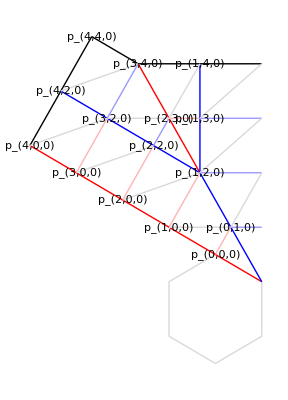

~/Desktop/sector.eps

```mathematica
Module[{r=2,h=2,m=6,cpset,ffset,pair},
cpset=Graphics[{
Style[Line[Table[Subscript[p, 0,0,k],{k,0,m-1}]],LightFold],
FlasherSector[p,r,h,0],
PtLabel/@FlasherFirstSectorVerticesDistinct[p,r,h]}]/.RulesCP[m];
ffset=Graphics3D[{
FlasherSector[pp,r,h,0],
PtLabel/@FlasherFirstSectorVerticesDistinct[pp,r,h]}]/.RulesFF[h,m,0.2];
pair=GraphicsRow[{cpset,ffset},Spacings->Scaled[-0.2]];
Print[pair];
Export["~/Desktop/sector.eps",pair,ImageSize->384] (* this gives a good relative size of the text labels *)
]
```

#### flasher-example.eps

```mathematica
Module[{r=2,h=2,m=6,af,gg},
af=AnalyzeFlatBottomFlasher[r,h,m,0.1];
gg=GraphicsGrid[af⟦3⟧,Spacings->{Scaled[-0.1],Scaled[-0.1]}];
Print[gg];
Export["~/Desktop/flasher-example.eps",gg,ImageSize->784] (* this gives a good relative size of the text labels *)
]
```

-Graphics-

~/Desktop/flasher-example.eps